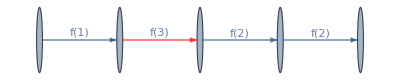

```mathematica
Graph[{1->2,2->3,3->4,4->5},EdgeLabels->{1->2->Placed[f[1],{0.5,{0.5,0.1}}],2->3->Placed[f[3],{0.5,{0.5,0.1}}],3->4->Placed[f[2],{0.5,{0.5,0.1}}],4->5->Placed[f[2],{0.5,{0.5,0.1}}]},EdgeStyle->{2->3->Red}]
```

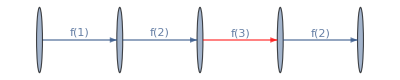

```mathematica
Graph[{1->2,2->3,3->4,4->5},EdgeLabels->{1->2->Placed[f[1],{0.5,{0.5,0.1}}],2->3->Placed[f[2],{0.5,{0.5,0.1}}],3->4->Placed[f[3],{0.5,{0.5,0.1}}],4->5->Placed[f[2],{0.5,{0.5,0.1}}]},EdgeStyle->{3->4->Red}]
```

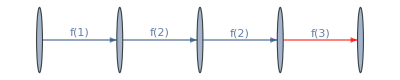

```mathematica
Graph[{1->2,2->3,3->4,4->5},EdgeLabels->{1->2->Placed[f[1],{0.5,{0.5,0.1}}],2->3->Placed[f[2],{0.5,{0.5,0.1}}],3->4->Placed[f[2],{0.5,{0.5,0.1}}],4->5->Placed[f[3],{0.5,{0.5,0.1}}]},EdgeStyle->{4->5->Red}]
```

```mathematica
f[n_]:=Style["f("<>ToString[n]<>")",Large]
```

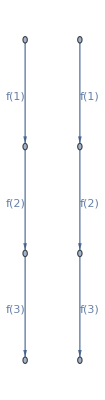

```mathematica
Graph[{1->2,2->3,3->4,5->6,6->7,7->8},EdgeLabels->{1->2->Placed[f[1],{0.5,{1.25,1}}],2->3->Placed[f[2],{0.5,{1.25,1}}],3->4->Placed[f[3],{0.5,{1.25,1}}],5->6->Placed[f[1],{0.5,{-0.25,1}}],6->7->Placed[f[2],{0.5,{-0.25,1}}],7->8->Placed[f[3],{0.5,{-0.25,1}}]}]
```

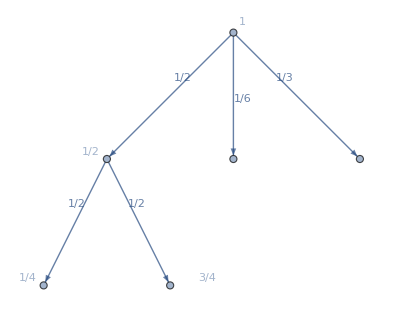

```mathematica
Graph[{1->2,1->3,1->4,2->5,2->6},
EdgeLabels->{1->2->Placed[Style["1/2",Large],{1/3,{2,1}}],
1->4->Placed[Style["1/3",Large],{1/3,{-0.75,1}}],
1->3->Placed[Style["1/6",Large],{0.5,{0,1}}],

2->5->Placed[Style["1/2",Large],{1/3,{1.5,1}}],
2->6->Placed[Style["1/2",Large],{1/3,{-0.5,1}}]
},

VertexLabels->{1->Style[1,Large],2->Placed[Style["1/2",Large],{{-0.5,2.25},{1,1}}],
5->Placed[Style["1/4",Large],{{-0.5,2.25},{1,1}}],
6->Placed[Style["3/4",Large],{{7,2.25},{1,1}}]
}
]
```

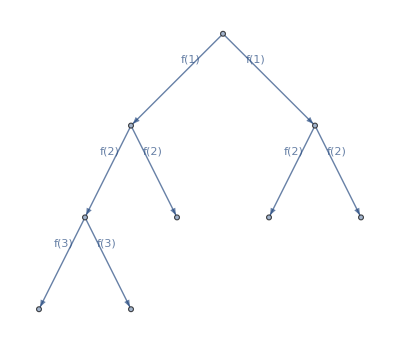

```mathematica
Graph[{1->2,1->3,2->4,2->5,4->6,4->7,3->8,3->9},
EdgeLabels->{
1->2->Placed[f[1],{0.25,{1.6,1}}],
1->3->Placed[f[1],{0.25,{-0.7,1}}],
2->4->Placed[f[2],{0.25,{1.4,1}}],
2->5->Placed[f[2],{0.25,{-0.5,1}}],
4->6->Placed[f[3],{0.25,{1.4,1}}],
4->7->Placed[f[3],{0.25,{-0.5,1}}],
3->8->Placed[f[2],{0.25,{1.4,1}}],
3->9->Placed[f[2],{0.25,{-0.5,1}}]
},
VertexCoordinates->{{10,10},{8,8},{12,8},{7,6},{9,6},{6,4},{8,4},{11,6},{13,6}}
]
```